```mathematica
(* System Potential of continous logistic *)
Clear["Global`*"]
```

```mathematica
(* Define model as differential eqn. *)
dNdt=r Ν (1-Ν/K)(Ν/A-1)
```

r Ν (-1+Ν/A) (1-Ν/K)

```mathematica
(* Specify some parameter values for plotting *)
parms={r->1,K->10,A->5};
```

```mathematica
dNdt/.parms
```

(1-Ν/10) (-1+Ν/5) Ν

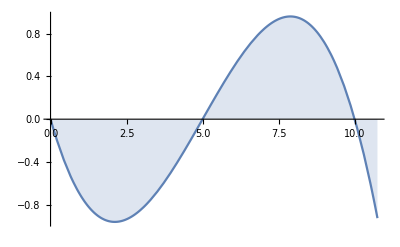

```mathematica
Plot[dNdt/.parms,{Ν,0,10.75},Filling->Axis]
```

```mathematica
(* Solve for equilibria *)
equil=Solve[dNdt==0,Ν];
%//TableForm
```

Ν→0
Ν→A
Ν→K

```mathematica
(* Derivative of dN/dt w.r.t. N*)
fDeriv=D[dNdt,Ν]//Expand
```

-r+(2 r Ν)/A+(2 r Ν)/K-(3 r Ν^2)/(A K)

```mathematica
(* Evaluate first derivative at each equilibrium *)
fDeriv=fDeriv/.equil//Simplify;
TableForm[{{equil,fDeriv,fDeriv/.parms}}]
```

Ν→0
Ν→A
Ν→K | -r
r-(A r)/K
r-(K r)/A | -1
1/2
-1

```mathematica
(* System Potential *)
pN=-Integrate[dNdt,Ν]//Expand
```

(r Ν^2)/2-(r Ν^3)/(3 A)-(r Ν^3)/(3 K)+(r Ν^4)/(4 A K)

```mathematica
pN=-∫dNdtⅆΝ//Expand
```

(r Ν^2)/2-(r Ν^3)/(3 A)-(r Ν^3)/(3 K)+(r Ν^4)/(4 A K)

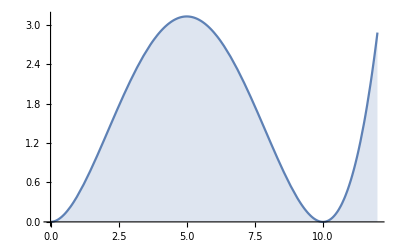

```mathematica
Plot[pN/.parms,{Ν,0,12},Filling->Axis]
```